# Superposition and Entanglement

We will discuss the concepts of quantum superposition and entanglement in more detail. We will show how a linear combination of quantum states can look different from one basis to another, and how this relates to whether states are separable or entangled. We will then explain how to test whether a state is entangled and how to quantify the amount of entanglement.

## Key Concepts

Superposition

Entanglement

GHZ state

Partial Trace

## Superposition and Entanglement

Superposition and entanglement are two fundamental characteristic traits of the quantum world. Superposition is a direct consequence of the linearity of quantum dynamics, while entanglement stems from the tensor-product structure of the underlying vector spaces together with the linearity.

Quantum superposition means a system existing in a linear combination of possible states. For example, consider x_+ state (eigenstate of Pauli-X with the eigenvalue +1). Note that x_+ is also called a uniform superposition, and it is the outcome of below circuit:

```mathematica
QuantumCircuitOperator["H"]["Diagram"]
```

-Graphics-

Check the final state of the circuit is a uniform superposition:

```mathematica
QuantumCircuitOperator["H"][]==QuantumState["+"]==QuantumState["UniformSuperposition"]
```

True

Show the Dirac notation in the corresponding basis:

```mathematica
QuantumState["+"]//TraditionalForm
```

1/(√2)0+1/(√2)1

This representation can also be misleading, because it is a linear combination (i.e., a quantum superposition) in the computational basis. If you rewrite the same state in a different basis, it may take a very different form.

Transform the state in the Pauli-X basis:

```mathematica
QuantumState[QuantumState["+"],"X"]//TraditionalForm
```

𝓍_+

Transform the state in the Pauli-Y basis:

```mathematica
QuantumState[QuantumState["+"],"Y"]//TraditionalForm
```

(1/2-ⅈ/2)𝓎_++(1/2+ⅈ/2)𝓎_−

Such a basis transformation can be done also for a composite state. For example, consider the state coming out of this circuit:

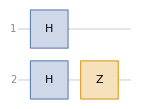

```mathematica
QuantumCircuitOperator[{"H","H"->2,"Z"->2}]["Diagram"]
```

Execute the circuit and show the Dirac notation of the state:

```mathematica
Ψ=QuantumCircuitOperator[{"H","H"->2,"Z"->2}][];
Ψ//TraditionalForm
```

1/2 00-1/201+1/2 10-1/211

If we transform this state to the Pauli-X basis, the form of the superposition changes. In particular, if the state is an eigenstate of X, it appears as a single basis vector in the  X-basis (so the superposition “disappears”). Otherwise, it remains a superposition—just expressed in terms of the X-basis vectors.

Show the state in the basis of X⊗X:

```mathematica
QuantumState[Ψ,"XX"]//TraditionalForm
```

𝓍_+𝓍_−

In other words, the representation of the state in the computational basis shows a superposition, so it is not immediately clear whether the state is a tensor product of two single-qubit states. However, if we rewrite the same state in another basis (for example, the eigenstates of Pauli-X) and the factorization becomes explicit, then the state is separable (not entangled) and can indeed be written as a tensor product. Note that separability is a property of the state itself, not the basis; a different basis can simply make that property more evident.

If a state is separable, we say it is not entangled.

```mathematica
QuantumEntangledQ[Ψ]
```

False

One way to confirm that a state is separable (for pure states) is to trace out a subsystem and check that the resulting reduced state is the same single-system state you specified in the product. Equivalently, both reduced states are pure, which indicates the overall state is a product (not entangled).

Tracing out qubit 2 gives x_+ as the reduced state:

```mathematica
QuantumPartialTrace[Ψ,{2}]==QuantumState["+"]
```

True

Tracing out qubit 1 gives x_- as the reduced state:

```mathematica
QuantumPartialTrace[Ψ,{1}]==QuantumState["-"]
```

True

Entanglement describes a quantum system in which parts of that system cannot be given complete, independent descriptions. In other words, the whole system has a definite state, but some individual parts may not have a definite state.

To create an entangled state, you will need a gate that is not separable. A famous gate that can be used is CNOT:

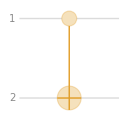
-Graphics-  ψ | CNOTψ
00 | 00
01 | 01
10 | 11
11 | 10

```mathematica
Row[{QuantumCircuitOperator["CNOT"]["Diagram"],"  ",TableForm[{TraditionalForm[#],TraditionalForm[QuantumCircuitOperator["CNOT"][#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","CNOTψ"}}]}]
```

That said, looking at the table above, the CNOT’s effect becomes visible only if qubit 1 (the control) has support on |0⟩ as well as |1⟩. In other words, we need a superposition of 0 and 1 for the control qubit. We can create such a superposition with a Hadamard gate or with an appropriate single-qubit rotation.

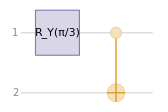

```mathematica
QuantumCircuitOperator[{"RY"[π/3],"CNOT"}]["Diagram"]
```

Calculate the final state of above circuit:

```mathematica
state=QuantumCircuitOperator[{"RY"[π/3],"CNOT"}][]
```

QuantumState[…]

Show it in the Dirac notation:

```mathematica
state//TraditionalForm
```

(√3)/2 00+1/2 11

Calculate the corresponding measurement probabilities:

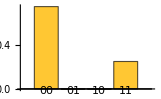

```mathematica
state["ProbabilitiesPlot"]
```

In this case, it isn’t trivial to tell whether the state is entangled. In the Wolfram Quantum Framework, you can test it using QuantumEntangledQ, which returns True if the state is entangled (with respect to the chosen partition) and False otherwise.

```mathematica
QuantumEntangledQ[state]
```

True

For multi-qubit systems, be sure to specify the partition of subsystems when you call QuantumEntangledQ, (always check the documentation pages).

Another way to test whether a state is entangled is as follows. First, compute the reduced states by performing partial traces. Then compare the tensor product of the reduced states with the original state. If they are the same, the state is not entangled; otherwise, it is entangled.

Generate the reduced state of qubit 1:

```mathematica
ρ1=QuantumPartialTrace[state,{2}];
```

Generate the reduced state of qubit 2:

```mathematica
ρ2=QuantumPartialTrace[state,{1}];
```

Compare the tensor product of the reduced states with the original state:

```mathematica
QuantumTensorProduct[ρ1,ρ2]==state
```

False

Since they are not the same, it means the original state was entangled state.

The above criterion is dependable for pure states. For mixed states, however, separability does not generally imply equality with the product of the marginals (many separable mixed states are mixtures of product states), so additional tests are needed.

Last but not least, given an entangled state, an interesting question is to quantify the entanglement. One common measure is called the generalized concurrence, which is a measure for the entanglement monotone. See the documentation page of QuantumEntanglementMonotone for more details.

Calculate the concurrence for the above state:

```mathematica
QuantumEntanglementMonotone[state]
```

(√3)/2

Calculate the concurrence for the Bell state:

```mathematica
QuantumEntanglementMonotone[QuantumState["Bell"]]
```

1

As you can see, the Bell state is maximally entangled—it exhibits the strongest possible two-qubit entanglement (e.g., one bit of entanglement entropy, concurrence equal to 1).

Entanglement can extend beyond only two qubits. The GHZ circuit is shown below:

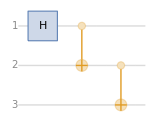

```mathematica
QuantumCircuitOperator["GHZ"]["Diagram"]
```

The outcome of above circuit is a state is usually called as GHZ state:

```mathematica
QuantumCircuitOperator["GHZ"][]//TraditionalForm
```

1/(√2)000+1/(√2)111

We also have GHZ as a named state in the Wolfram quantum framework:

```mathematica
QuantumCircuitOperator["GHZ"][]==QuantumState["GHZ"]
```

True

Check GHZ state is an entangled state:

```mathematica
QuantumEntangledQ[QuantumState["GHZ"]]
```

True

Calculate its concurrence:

```mathematica
QuantumEntanglementMonotone[QuantumState["GHZ"]]
```

1

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]